```mathematica
(* set up the Levy alpha-stable SDE *)
α=1;
(* drift *)
f[x_] := Sin[x]
(* constant diffusion *)
g=0.25;
```

```mathematica
nsamp=1;
dt = 0.01;
numsteps=400;
ns = numsteps;
mcsol=Table[0,ns+1];
mcsol[[1]]=0.1; (* initial condition *)
For[i=1,i≤ns,i+=1,
mcsol[[i+1]] =mcsol[[i]]+ (dt*f[mcsol[[i]]] +  RandomVariate[StableDistribution[1,α,0.0,0.0,dt g],nsamp]);
]
```

```mathematica
Flatten[mcsol][[1;;100]]
```

{0.1,0.0976788,0.0940961,0.0958354,0.0923348,0.0947097,0.0944191,0.0966252,0.0957446,0.150339,0.146201,0.153439,0.156503,0.152955,0.159707,0.143339,0.146919,0.160351,0.162222,0.162935,0.166655,0.170846,0.170416,0.161494,0.161717,0.150086,0.150616,0.0941785,0.0822958,0.0843316,0.0915632,0.0922597,0.0913584,0.0952263,0.105698,0.103183,0.103496,0.103553,0.106,0.109467,0.111241,0.112079,0.113692,0.121668,0.120521,0.120451,0.55864,0.562969,0.572268,0.577279,0.57646,0.581605,0.581021,0.590257,0.593339,0.598765,0.603287,0.6103,0.61808,0.60703,0.610634,0.596847,0.603253,0.612916,0.618167,0.63647,0.645188,0.64727,0.648826,0.64802,0.65579,0.660241,0.651924,0.652029,0.659972,0.663367,0.669551,0.681654,0.684065,0.690137,0.692998,0.699466,0.713731,0.724776,0.768594,0.782036,0.786425,0.766208,0.773549,0.781243,0.786114,0.793787,0.797738,0.80525,0.815357,0.81925,0.803049,0.790884,0.799026,0.80499}

```mathematica
tvec=Table[j*dt,{j,0,numsteps}];
```

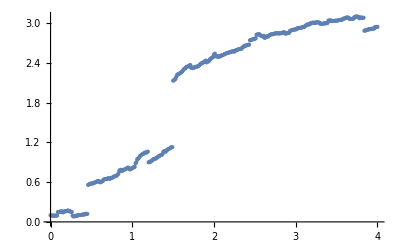

```mathematica
ListPlot[Transpose[{tvec,Flatten[mcsol]}]]
```

```mathematica
Export["mcsol.csv",mcsol]
```

mcsol.csv